```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
<<MaTeX`
```

```mathematica
F1[n_,q_,z_,α_]:=NIntegrate[1/(8 π^3)x^n(((√(x^2+z^2))^(q-1))/(Exp[√(x^2+z^2)-α]+1)+((√(x^2+z^2))^(q-1))/(Exp[√(x^2+z^2)+α]+1)),{x,0,∞},PrecisionGoal->10]
```

```mathematica
Ka[z_]:=-BesselK[0,z]/z+BesselK[1,z]-((2+z^2) BesselK[1,z])/z^2(*Here z=m/T*)
```

```mathematica
V[z_]:=(Simplify[-(z)^3*Exp[z]Ka[z]])^(-1/3)(* Here V[z]=T*(Subscript[λ, th]), T is temperature and Subscript[λ, th] is the thermal wavelength *)
Lth[T_,z_]:=((2*π^2)^(1/3)V[z])/T(*GeV^-1*)
```

```mathematica
MCC000i[ξ_,λ_,z_,α_]:=(ξ Exp[-ξ^2/4]*(2*π^2)^(4/3)*(V[z])^4)/(16*(√π)^3*(λ)^4)*1;
MCG000i[ξ_,λ_,z_,α_]:=MCC000i[ξ,λ,z,α]+(ξ Exp[-ξ^2/4]*(2*π^2)^(4/3)*(V[z])^4)/(16*(√π)^3*(λ)^4)(1+1/(2λ z)^2*(5/2-ξ^2/4)*1/(F1[4,0,z,α]/3+F1[2,2,z,α])*(F1[4,0,z,α]/3+2 z^2 F1[2,0,z,α]));
(* Here, ξ=y/σ,λ=σ*T and V[z]=T*(Subscript[λ, th]) *)
```

```mathematica
lx=8;
nx=40;
dx=(lx)/nx;
dptx=Table[N[(i*dx)],{i,0,(nx)}];
ly=1.4;
ny=40;
dy=(ly-0.01)/ny;
dpty=Table[0.01+N[(i*dy)],{i,0,(ny)}];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}\\usepackage{amsmath}\\everymath{\\color{black}}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color}\usepackage{amsmath}\everymath{\color{black}}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

## CAN (α=1) :

```mathematica
can00={};
can01={};
can02={};
For[i=1, i<(nx+1),i++,
	For[j=1,j<(ny+1),j++,
		AppendTo[can00,{dptx[[i]],dpty[[j]],Log[10,MCC000i[dptx[[i]],dpty[[j]],0.1,1] ]}];
		AppendTo[can01,{dptx[[i]],dpty[[j]],Log[10,MCC000i[dptx[[i]],dpty[[j]],1,1] ]}];
		AppendTo[can02,{dptx[[i]],dpty[[j]],Log[10,MCC000i[dptx[[i]],dpty[[j]],10,1] ]}]
]
]
```

```mathematica
colors={Darker[RGBColor["#1C2770"]],RGBColor["#2B5781"],RGBColor["#3D7F8B"],RGBColor["#519C89"],RGBColor["#64B583"],RGBColor["#81C77C"],RGBColor["#C7DD72"],RGBColor["#E9E570"]}
```

{RGBColor[0.07320261437908497, 0.1019607843137255, 0.2928104575163399],RGBColor[0.16862745098039217, 0.3411764705882353, 0.5058823529411764],RGBColor[0.23921568627450981, 0.4980392156862745, 0.5450980392156862],RGBColor[0.3176470588235294, 0.611764705882353, 0.5372549019607843],RGBColor[0.39215686274509803, 0.7098039215686275, 0.5137254901960784],RGBColor[0.5058823529411764, 0.7803921568627451, 0.48627450980392156],RGBColor[0.7803921568627451, 0.8666666666666667, 0.4470588235294118],RGBColor[0.9137254901960784, 0.8980392156862745, 0.4392156862745098]}

```mathematica
can00//Length
```

1600

```mathematica
c1=ListContourPlot[Join[can00[[All,{1,2,3}]]],PlotRange-> {Full,Full,Full},PlotLegends->Automatic (*,ColorFunction->"BlueGreenYellow"*), Contours->{-6,-4,-2,0,2,4,6},ContourShading-> colors, PlotLabel->Style[MaTeX["\\log_{10}{|\\mathcal{C}_{00,0j}^{Can}|}",FontSize->20]],FrameLabel->{Style[MaTeX["\\xi",FontSize->20]],Style[MaTeX["\\lambda",FontSize->20]]},ContourStyle->White,BaseStyle->10,FrameTicksStyle->Automatic ,PlotRangePadding->0,Epilog->{Text[MaTeX["z=0.1,\, \\alpha=1\,\,",FontSize->16],Scaled[{0.18,0.95}],Background->LightBlue],
Text[MaTeX["\\color{white}{-6}",FontSize->16],Scaled[{0.9,0.85}]],
Text[MaTeX["\\color{white}{-4}",FontSize->16],Scaled[{0.7,0.81}]],
Text[MaTeX["\\color{white}{-2}",FontSize->16],Scaled[{0.47,0.72}]],
Text[MaTeX["\\color{white}{0}",FontSize->16],Scaled[{0.23,0.49}]],
Text[MaTeX["\\color{black}{2}",FontSize->16],Scaled[{0.16,0.17}]],
Text[MaTeX["\\color{black}{4}",FontSize->16],Scaled[{0.15,0.065}]],
Text[MaTeX["\\color{black}{6}",FontSize->16],Scaled[{0.3,0.025}]]}];
c2=ListContourPlot[Join[can01[[All,{1,2,3}]]],PlotRange-> {Full,Full,Full},PlotLegends->Automatic, Contours->{-6,-4,-2,0,2,4,6},ContourShading-> colors,PlotLabel->Style[MaTeX["\\log_{10}{|\\mathcal{C}_{00,0j}^{Can}|}",FontSize->20]],FrameLabel->{Style[MaTeX["\\xi",FontSize->20]],Style[MaTeX["\\lambda",FontSize->20]]},ContourStyle->White,BaseStyle->10,FrameTicksStyle->Automatic  ,PlotRangePadding->0,Epilog->{Text[MaTeX["z=1,\, \\alpha=1\,\,",FontSize->16],Scaled[{0.163,0.95}],Background->LightBlue],
Text[MaTeX["\\color{white}{-6}",FontSize->16],Scaled[{0.85,0.91}]],
Text[MaTeX["\\color{white}{-4}",FontSize->16],Scaled[{0.65,0.87}]],
Text[MaTeX["\\color{white}{-2}",FontSize->16],Scaled[{0.38,0.78}]],
Text[MaTeX["\\color{white}{0}",FontSize->16],Scaled[{0.18,0.4}]],
Text[MaTeX["\\color{black}{2}",FontSize->16],Scaled[{0.16,0.14}]],
Text[MaTeX["\\color{black}{4}",FontSize->16],Scaled[{0.15,0.05}]]}];
c3=ListContourPlot[Join[can02[[All,{1,2,3}]]],PlotRange-> {Full,Full,Full},PlotLegends->Automatic, Contours->{-6,-4,-2,0,2,4,6},ContourShading-> colors,PlotLabel->Style[MaTeX["\\log_{10}{|\\mathcal{C}_{00,0j}^{Can}|}",FontSize->20]],FrameLabel->{Style[MaTeX["\\xi",FontSize->20]],Style[MaTeX["\\lambda",FontSize->20]]},ContourStyle->White,BaseStyle->10,FrameTicksStyle->Automatic ,PlotRangePadding->0 ,Epilog->{Text[MaTeX["z=10,\, \\alpha=1\,\,",FontSize->16],Scaled[{0.174,0.95}],Background->LightBlue],
Text[MaTeX["\\color{white}{-8}",FontSize->16],Scaled[{0.9,0.92}]],
Text[MaTeX["\\color{white}{-6}",FontSize->16],Scaled[{0.72,0.9}]],
Text[MaTeX["\\color{white}{-4}",FontSize->16],Scaled[{0.48,0.82}]],
Text[MaTeX["\\color{white}{-2}",FontSize->16],Scaled[{0.18,0.57}]],
Text[MaTeX["\\color{white}{0}",FontSize->16],Scaled[{0.16,0.19}]],
Text[MaTeX["\\color{black}{2}",FontSize->16],Scaled[{0.15,0.07}]],
Text[MaTeX["\\color{black}{4}",FontSize->16],Scaled[{0.25,0.02}]]}];
```

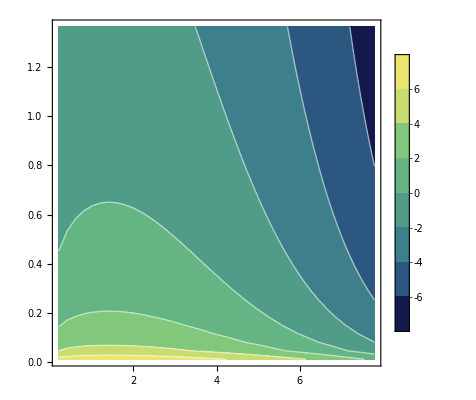

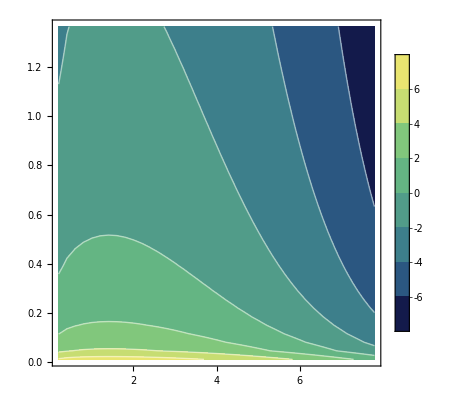

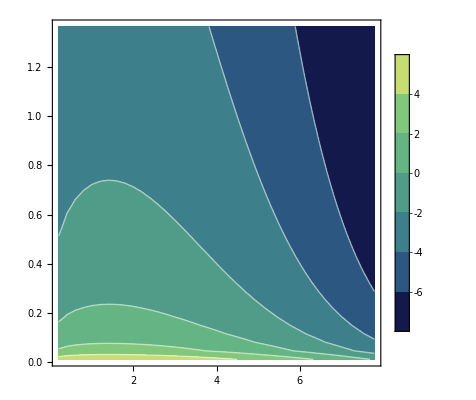

```mathematica
pcan00=Show[c1]
pcan01=Show[c2]
pcan02=Show[c3]
```

```mathematica
Export["can0_0m.pdf",pcan00];
Export["can0_1m.pdf",pcan01];
Export["can0_2m.pdf",pcan02];
```

## GLW (α=1) :

```mathematica
glw00={};
glw01={};
glw02={};
For[i=1, i<(nx+1),i++,
	For[j=1,j<(ny+1),j++,
		AppendTo[glw00,{dptx[[i]],dpty[[j]],Log[10,Abs[MCG000i[dptx[[i]],dpty[[j]],0.1,1] ]]}];
		AppendTo[glw01,{dptx[[i]],dpty[[j]],Log[10,Abs[MCG000i[dptx[[i]],dpty[[j]],1,1]]]}];
		AppendTo[glw02,{dptx[[i]],dpty[[j]],Log[10,Abs[MCG000i[dptx[[i]],dpty[[j]],10,1]]]}]
]
]
```

```mathematica
g1=ListContourPlot[glw00[[All,{1,2,3}]],PerformanceGoal-> "Quality",PlotLegends->Automatic,Contours->{-6,-4,-2,0,2,4,6},ContourShading-> colors,PlotLabel->Style[MaTeX["\\log_{10}{|\\mathcal{C}_{00,0j}^{GLW}|}",FontSize->20]],FrameLabel->{Style[MaTeX["\\xi",FontSize->20]],Style[MaTeX["\\lambda",FontSize->20]]},ContourStyle->White,BaseStyle->10,FrameTicksStyle->Automatic ,PlotRangePadding->0,Epilog->{Text[MaTeX["z=0.1,\, \\alpha=1\,\,",FontSize->16],Scaled[{0.182,0.95}],Background->LightBlue],
Text[MaTeX["\\color{white}{-4}",FontSize->16],Scaled[{0.94,0.91}]],
Text[MaTeX["\\color{white}{-2}",FontSize->16],Scaled[{0.72,0.88}]],
Text[MaTeX["\\color{white}{0}",FontSize->16],Scaled[{0.3,0.77}]],
Text[MaTeX["\\color{black}{2}",FontSize->16],Scaled[{0.18,0.42}]],
Text[MaTeX["\\color{black}{4}",FontSize->16],Scaled[{0.15,0.21}]],
Text[MaTeX["\\color{black}{6}",FontSize->16],Scaled[{0.15,0.1}]],
Text[MaTeX["\\color{black}{8}",FontSize->16],Scaled[{0.16,0.043}]]}];
g2=ListContourPlot[glw01[[All,{1,2,3}]],PerformanceGoal-> "Quality",PlotLegends->Automatic,Contours->{-6,-4,-2,0,2,4,6},ContourShading-> colors,PlotLabel->Style[MaTeX["\\log_{10}{|\\mathcal{C}_{00,0j}^{GLW}|}",FontSize->20]],FrameLabel->{Style[MaTeX["\\xi",FontSize->20]],Style[MaTeX["\\lambda",FontSize->20]]},ContourStyle->White,BaseStyle->10,FrameTicksStyle->Automatic  ,PlotRangePadding->0,Epilog->{Text[MaTeX["z=1,\, \\alpha=1\,\,",FontSize->16],Scaled[{0.163,0.95}],Background->LightBlue],
Text[MaTeX["\\color{white}{-6}",FontSize->16],Scaled[{0.87,0.91}]],
Text[MaTeX["\\color{white}{-4}",FontSize->16],Scaled[{0.68,0.87}]],
Text[MaTeX["\\color{white}{-2}",FontSize->16],Scaled[{0.43,0.8}]],
Text[MaTeX["\\color{white}{0}",FontSize->16],Scaled[{0.16,0.5}]],
Text[MaTeX["\\color{black}{2}",FontSize->16],Scaled[{0.15,0.2}]],
Text[MaTeX["\\color{black}{4}",FontSize->16],Scaled[{0.15,0.095}]],
Text[MaTeX["\\color{black}{6}",FontSize->16],Scaled[{0.2,0.043}]]}];
g3=ListContourPlot[glw02[[All,{1,2,3}]],PerformanceGoal-> "Quality",PlotLegends->Automatic,Contours->{-6,-4,-2,0,2,4,6},ContourShading-> colors,PlotLabel->Style[MaTeX["\\log_{10}{|\\mathcal{C}_{00,0j}^{GLW}|}",FontSize->20]],FrameLabel->{Style[MaTeX["\\xi",FontSize->20]],Style[MaTeX["\\lambda",FontSize->20]]},ContourStyle->White,BaseStyle->10,FrameTicksStyle->Automatic ,PlotRangePadding->0 ,Epilog->{Text[MaTeX["z=10,\, \\alpha=1\,\,",FontSize->16],Scaled[{0.175,0.95}],Background->LightBlue],
Text[MaTeX["\\color{white}{-8}",FontSize->16],Scaled[{0.92,0.94}]],
Text[MaTeX["\\color{white}{-6}",FontSize->16],Scaled[{0.75,0.92}]],
Text[MaTeX["\\color{white}{-4}",FontSize->16],Scaled[{0.51,0.86}]],
Text[MaTeX["\\color{white}{-2}",FontSize->16],Scaled[{0.16,0.67}]],
Text[MaTeX["\\color{white}{0}",FontSize->16],Scaled[{0.16,0.225}]],
Text[MaTeX["\\color{black}{2}",FontSize->16],Scaled[{0.15,0.09}]],
Text[MaTeX["\\color{black}{4}",FontSize->16],Scaled[{0.2,0.029}]]}];
```

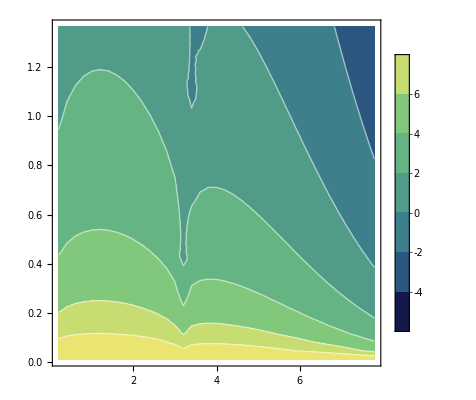

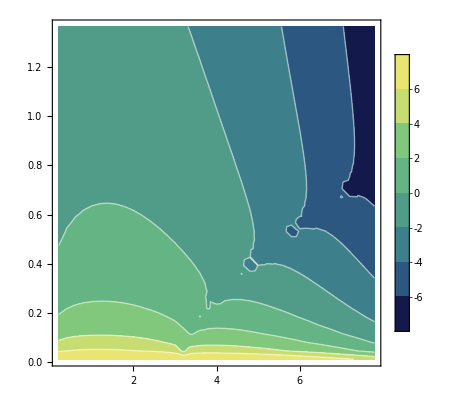

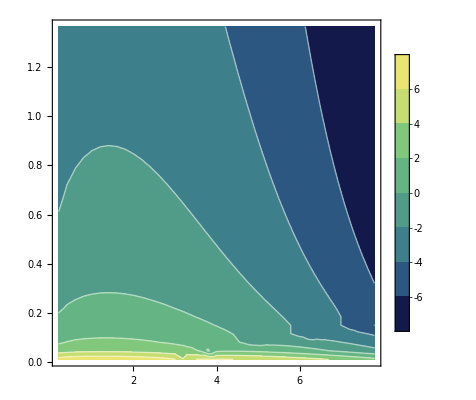

```mathematica
pglw00=Show[g1]
pglw01=Show[g2]
pglw02=Show[g3]
```

```mathematica
Export["glw0_0m.pdf",pglw00];
Export["glw0_1m.pdf",pglw01];
Export["glw0_2m.pdf",pglw02];
```

## Other Plots :

```mathematica
Cz=LogLinearPlot[{MCC000i[1,1,z,1],MCG000i[1,1,z,1]},{z,0.01,100},
 PlotRange->{0,2},Frame->True,PlotStyle->{Blue,{Dashed,Red}},FrameLabel->{Style[MaTeX["m/T",FontSize->16]],Style[MaTeX["\\log_{10}{|\\mathcal{C}_{00,0j}|}",FontSize->16]]},
PlotRangePadding->0.03 ,PlotTheme->"Detailed", PlotLegends->Placed[LineLegend[{MaTeX["Can"],MaTeX["GLW"]},LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.7]],RoundingRadius->4,Background->RGBColor[.95,.95,.95,0.75]]&)],{0.82,0.8}]];
```

```mathematica
Ca=LogLinearPlot[{MCC000i[1,1,1,α],MCG000i[1,1,1,α]},{α,0.01,100},
 PlotRange->{0.06,0.2},Frame->True,PlotStyle->{Blue,{Dashed,Red}},FrameLabel->{Style[MaTeX["\\mu/T",FontSize->16]],Style[MaTeX["\\log_{10}{|\\mathcal{C}_{00,0j}|}",FontSize->16]]},
PlotRangePadding->0.03 ,PlotTheme->"Detailed", PlotLegends->Placed[LineLegend[{MaTeX["Can"],MaTeX["GLW"]},LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.7]],RoundingRadius->4,Background->RGBColor[.95,.95,.95,0.75]]&)],{0.82,0.8}]];
```

```mathematica
pla=Show[Ca];
plz=Show[Cz];
```

```mathematica
Export["pdfa.pdf",pla];
Export["pdfz.pdf",plz];
```

```mathematica
MCG000i[1,1,500,1]
```

2.74703×10^-6

```mathematica
MCG000i[1,1,300,1]
```

7.60534×10^-6

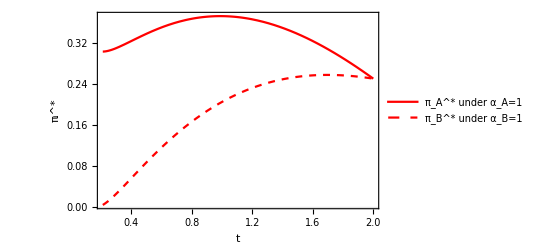

```mathematica
Plot[{((3 t+1/2)^2 (1-2 t 1/4))/(18 t)+2 t^3 (1)^2 (1/4)^3,((3 t-1/2)^2 (1-2 t (1/4)))/(18 t)+2 t^3 (1)^2 (1/4)^3},{t,1/6 (3-Sqrt[3]),2},PlotTheme->"Scientific",PlotRange->All,FrameLabel->{HoldForm[t],HoldForm[SubsuperscriptBox["π","i","*"]//DisplayForm]},PlotStyle->{Red,{Dashed,Red}},PlotLegends->Placed[LineLegend[{"\!\(\*SubsuperscriptBox[\(π\), \(A\), \(*\)]\) under \!\(\*SubscriptBox[\(α\), \(A\)]\)=1","\!\(\*SubsuperscriptBox[\(π\), \(B\), \(*\)]\) under \!\(\*SubscriptBox[\(α\), \(B\)]\)=1"},LegendLayout->Function[{x},Grid[x,Spacings->{0.6,0},Alignment->Left]],LegendMarkerSize->{22,12},LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4,Background->RGBColor[.95,.95,.95,1]]&)],{0.75,0.2}]]
```

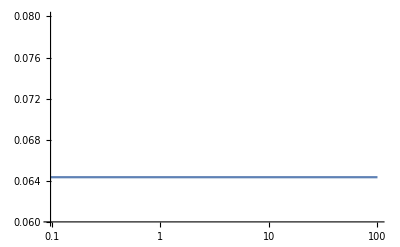

```mathematica
LogLinearPlot[{MCC000i[1,1,1,α],MCG000i[1,1,1,α]},{α,0,100}, PlotRange->{0.06,0.08}]
```

```mathematica
|
```